1.66667-0.75 Cos[t]-0.916667 Cos[2 t]-1.01036 Sin[t]+0.721688 Sin[2 t]

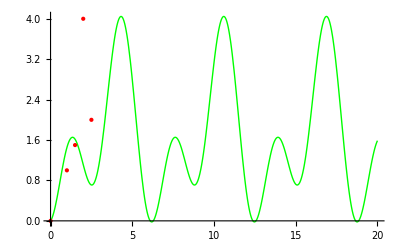

```mathematica
y[t_]:=a0+a1*Cos[t]+b1*Sin[t]+a2*Cos[2t]+b2*Sin[2t];
solY=Solve[{y[0]==0,y[2Pi/3]==1,y[Pi]==1.5,y[4Pi/3]==4,y[5Pi/3]==2},{a0,a1,a2,b1,b2}];
y[t_]=y[t]/.solY[[1]]
points=ListPlot[{{0,0},{1,1},{1.5,1.5},{2,4},{2.5,2}},PlotStyle->Red];
(*plotX=Plot[x[t],{t,0,2.5}];*)
plotY=Plot[y[t],{t,0,20},PlotStyle->Green,PlotRange->All];
Show[plotY,points]
```